Ok we’ll start by writing a sorting algorithm that sorts at random.

```mathematica
n=100;
A=Table[i,{i,1,10}]
B=Table[0,{i,1,10}];
Do[
x=Random[Integer,{1,10}];
y=Random[Integer,{1,10}];
If[A[[y]]<A[[x]],B[[x]]=B[[x]]+1],{n}]
B
```

{1,2,3,4,5,6,7,8,9,10}

{0,1,3,2,6,2,7,6,4,11}

This is not a good method. Even if n is 100 times larger than the population size, we have pathological behavior even with perfect case distinction. 

I think we will need some sort of “losers vs losers” and “winners vs winners.” For implemtation purposes, I think we can only think about immideate losing/winning.

```mathematica
n=100;
A=Table[i,{i,1,10}]
B=Table[0,{i,1,10}];
W = A;
Do[
x=Random[Integer,{1,10}];
If[MemberQ[W,x],
y=W[[Random[Integer,{1,Length[W]}]]],
y=Complement[A,W][[Random[Integer,{1,Length[Complement[A,W]]}]]]];
If[A[[y]]<A[[x]],
B[[x]]=B[[x]]+1;
W=Union[W,{x}], W=Complement[W,{x}]],
{n}]
B
```

{1,2,3,4,5,6,7,8,9,10}

{0,5,3,0,3,5,5,4,7,7}

Also no good. Now we’ll check out winners vs losers.

```mathematica
n=100;
A=Table[i,{i,1,10}]
B=Table[0,{i,1,10}];
W = {1,3,5,7,9};
Do[
x=Random[Integer,{1,10}];
If[MemberQ[W,x],
y=Complement[A,W][[Random[Integer,{1,Length[Complement[A,W]]}]]],
y=W[[Random[Integer,{1.,Length[W]}]]]
];

If[A[[y]]<A[[x]],
B[[x]]=B[[x]]+1;
W=Union[W,{x}], W=Complement[W,{x}]],
{n}]
B2 = B
```

{1,2,3,4,5,6,7,8,9,10}

{0,0,0,0,9,6,12,10,14,8}

Can we add them?

```mathematica
n=5000;
A=Table[i,{i,1,10}]
B=Table[0,{i,1,10}];
W = A;
Do[
x=Random[Integer,{1,10}];
If[MemberQ[W,x],
y=W[[Random[Integer,{1.,Length[W]}]]],
y=Complement[A,W][[Random[Integer,{1,Length[Complement[A,W]]}]]]];
If[A[[y]]<A[[x]],
B[[x]]=B[[x]]+1;
W=Union[W,{x}], W=Complement[W,{x}]],
{n}]
B1 = B;

B=Table[0,{i,1,10}];
W = {1,3,5,7,9};
Do[
x=Random[Integer,{1,10}];
If[MemberQ[W,x],
y=Complement[A,W][[Random[Integer,{1,Length[Complement[A,W]]}]]],
y=W[[Random[Integer,{1.,Length[W]}]]]
];

If[A[[y]]<A[[x]],
B[[x]]=B[[x]]+1;
W=Union[W,{x}], W=Complement[W,{x}]],
{n}]
B2 = B;
B1
B2
B1+B2
```

{1,2,3,4,5,6,7,8,9,10}

{0,80,118,170,200,207,261,278,317,318}

{0,0,3,0,510,492,485,531,486,500}

{0,80,121,170,710,699,746,809,803,818}

Now let’s try to sort into bins - those that have been compared, and those that have not. Each round the bin will “reset” and we’ll draw from the less-compared bin.

```mathematica
n=100;
A=Table[i,{i,1,10}]
B=Table[0,{i,1,10}];
Pre =A;
Post={};
Do[
If[Length[Pre]==0,Pre=A;Post={}];
x=Pre[[Random[Integer,{1,Length[Pre]}]]];
y=Pre[[Random[Integer,{1,Length[Pre]}]]];
If[A[[y]]<A[[x]],
B[[x]]=B[[x]]+1;  
Post=Sort[Join[Post,{A[[x]],A[[y]]}]];
Pre=Complement[Pre,{A[[x]],A[[y]]}]],
{n}]
B
```

{1,2,3,4,5,6,7,8,9,10}

{0,1,4,2,3,4,3,2,4,5}

## THE ONES THAT SORT OF WORK!

Ok now we’ll add less if it is an expected win. This is based on the idea of the Elo ranking system

```mathematica
n=2000;
l = 10;
A=Table[i,{i,1,l}]
B=Table[1,{i,1,l}];
Do[
x=Random[Integer,{1,Length[A]}];
y=Random[Integer,{1,Length[A]}];
If[A[[y]]<A[[x]],
B[[x]]=Floor[B[[x]]+B[[y]]/B[[x]]]],  
{n}]
B
```

{1,2,3,4,5,6,7,8,9,10}

{1,2,3,4,5,6,7,8,9,10}

Same but sorting by bins:

```mathematica
n=1000;
k=1;
A=Table[i,{i,1,10}]
B=Table[1,{i,1,10}];
Pre =A;
Post={};
Do[
If[Length[Pre]==0,Pre=A;Post={}];
x=Pre[[Random[Integer,{1,Length[Pre]}]]];
y=Pre[[Random[Integer,{1,Length[Pre]}]]];
If[A[[y]]<A[[x]],
B[[x]]=Floor[B[[x]]+k*B[[y]]/B[[x]]];  
Post=Sort[Join[Post,{A[[x]],A[[y]]}]];
Pre=Complement[Pre,{A[[x]],A[[y]]}]
],
{n}]
B
```

{1,2,3,4,5,6,7,8,9,10}

{1,2,3,4,5,6,7,8,9,10}

Same thing - but now there are repeats

```mathematica
s=1000;
n=100000;
A=Flatten[Table[Table[i,{j,1,200}],{i,1,s/200}]];
Tally[A]
B=Table[1,{i,1,s}];
Do[
x=Random[Integer,{1,Length[A]}];
y=Random[Integer,{1,Length[A]}];
If[A[[y]]<A[[x]],
B[[x]]=Floor[B[[x]]+(B[[y]])/B[[x]]]],  
{n}]
Tally[B]
```

{{1,200},{2,200},{3,200},{4,200},{5,200}}

{{1,200},{2,200},{3,200},{4,200},{5,200}}

We’re only counting one of the winners previously...  now we’re counting both... Not sure if it helps.

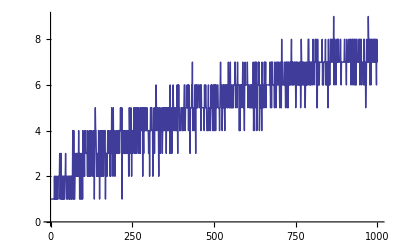

```mathematica
n=10000;
l = 1000;
k=1;
A=Table[i,{i,1,l}];
B=Table[1,{i,1,l}];
Do[
x=Random[Integer,{1,Length[A]}];
y=Random[Integer,{1,Length[A]}];
If[A[[y]]<A[[x]],
B[[x]]=Floor[B[[x]]+k*B[[y]]/B[[x]]]];
If[A[[y]]>A[[x]],
B[[y]]=Floor[B[[y]]+k*B[[x]]/B[[y]]]],  
{n}]
ListLinePlot[B]
```

Now - punish... This does not seem to help....

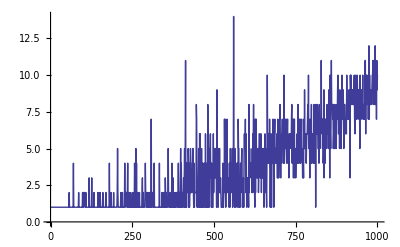

```mathematica
n=10000;
l = 1000;
A=Table[i,{i,1,l}];
B=Table[1,{i,1,l}];
Do[
x=Random[Integer,{1,Length[A]}];
y=Random[Integer,{1,Length[A]}];
If[
A[[y]]<A[[x]],
B[[x]]=Floor[B[[x]]+1.5B[[y]]/B[[x]]];
B[[y]]=Max[Floor[B[[y]]-B[[y]]/B[[x]]],1]
];
If[
A[[y]]>A[[x]],
B[[y]]=Floor[B[[y]]+1.5B[[x]]/B[[y]]];
B[[x]]=Max[Floor[B[[x]]-B[[x]]/B[[y]]],1]],  
{n}]
ListLinePlot[B]
```

## Jim’s Idea

So maybe something like this would work.

Let N = number of students.

Start with a N-by-N matrix A where all the entries are 0.5.  Here, A_ij
is the probability that i’s answer is better than j’s answer.

Pick an entry A_ij which is closest to 0.5.

Ask the user whether i or j is better; depending on the answer, set A_ij
= 0.9 and A_ji = 0.1 or vice versa.

Replace A by A*A/N (or by A^3/N^2, or by...)

Repeat a whole bunch of times.

Then we can average the columns to get a numeric score for each student.

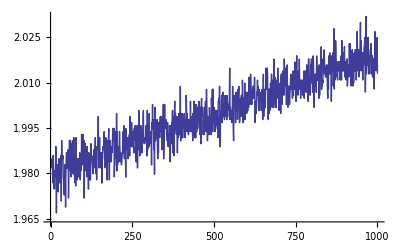

```mathematica
n=10000;
l = 1000;
A=Table[i,{i,1,l}];
M = ConstantArray[.5,{l,l}];
Do[
x=Random[Integer,{1,Length[A]}];
y=Random[Integer,{1,Length[A]}];
If[A[[y]]<A[[x]],
M[[x,y]]=.00001;
M[[y,x]]=.99999];
If[A[[y]]>A[[x]],
M[[x,y]]=.99999;
M[[y,x]]=.00001],  
{n}]
M=Inverse[IdentityMatrix[l] - M/l];
ListLinePlot[Table[l*Mean[Table[M[[i,j]],{i,1,l}]],{j,1,l}]]
```

## Compare the matrix method with the voting method.

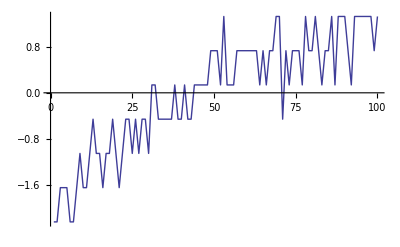

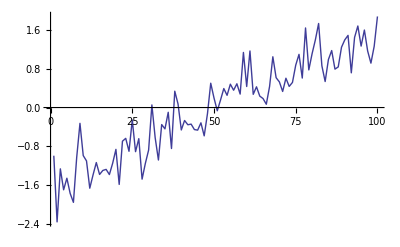

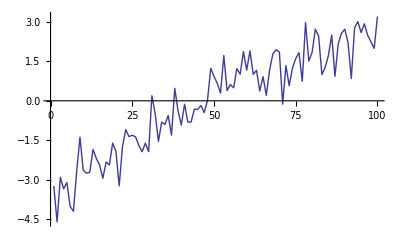

```mathematica
n=1000;
l = 100;
A=Table[i,{i,1,l}];
B=Table[1,{i,1,l}];
M = ConstantArray[.5,{l,l}];
Do[
x=Random[Integer,{1,Length[A]}];
y=Random[Integer,{1,Length[A]}];
If[A[[y]]<A[[x]],
M[[x,y]]=.00001;
M[[y,x]]=.99999];
If[A[[y]]>A[[x]],
M[[x,y]]=.99999;
M[[y,x]]=.00001];
If[A[[y]]<A[[x]],
B[[x]]=Floor[B[[x]]+k*B[[y]]/B[[x]]]];
If[A[[y]]>A[[x]],
B[[y]]=Floor[B[[y]]+k*B[[x]]/B[[y]]]],  
{n}]
M=Inverse[IdentityMatrix[l] - M/l];
F=Table[l*Mean[Table[M[[i,j]],{i,1,l}]],{j,1,l}];
ListLinePlot[(B-Mean[B])/StandardDeviation[B]]
ListLinePlot[(F-Mean[F])/StandardDeviation[F]]
ListLinePlot[(B-Mean[B])/StandardDeviation[B]+(F-Mean[F])/StandardDeviation[F]]
```

## Random Pairwise with Weighted Scores, imperfect scoring